# Tips & Tricks: Mathematica for Research

## Lecture 4 (20/04/2026)

```mathematica
Quit[]
```

```mathematica
SetOptions[EvaluationNotebook[],Magnification->1.75]
```

## From last time...

### AutoSave

```mathematica
ResourceFunction["SetNotebookAutoSaveTime"][120](*Save every 2min*)
```

```mathematica
SetOptions[EvaluationNotebook[],CellProlog:>(NotebookSave[])](*Save before Evaluating*)
```

### Matrices & Arrays

```mathematica
({{□, □, □, □}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}})(* Start with () and press Ctrl+Enter to add row / Ctrl+, to add column*)
```

```mathematica
SparseArray[{{2,4}->1,{5,3}->-1},{5,5}]//MatrixForm (*Good for arrays/matrices where most entries are zero; or when they are given by rules*)
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0)

```mathematica
(* Example: E8×E8 Cartan Matrix *)
matrix=SparseArray[{{i_,j_}:>2/;i==j,{i_,j_}:>-1/;Or[j==i+1&&j<8,i==j+1&&i<8],{5,8}->-1,{8,5}->-1},{8,8}]
```

SparseArray[…]

```mathematica
newmatrix=(matrix//Normal)(*Normal[] turns SparseArray into a 'normal' array*)
```

{{2,-1,0,0,0,0,0,0},{-1,2,-1,0,0,0,0,0},{0,-1,2,-1,0,0,0,0},{0,0,-1,2,-1,0,0,0},{0,0,0,-1,2,-1,0,-1},{0,0,0,0,-1,2,-1,0},{0,0,0,0,0,-1,2,0},{0,0,0,0,-1,0,0,2}}

```mathematica
matrix//FullForm
newmatrix//FullForm
```

SparseArray[Automatic,List[8,8],0,List[1,List[List[0,2,5,8,11,15,18,20,22],List[List[2],List[1],List[1],List[3],List[2],List[2],List[4],List[3],List[4],List[5],List[3],List[6],List[4],List[5],List[8],List[7],List[5],List[6],List[7],List[6],List[5],List[8]]],List[-1,2,-1,-1,2,-1,-1,2,2,-1,-1,-1,-1,2,-1,-1,-1,2,2,-1,-1,2]]]

List[List[2,-1,0,0,0,0,0,0],List[-1,2,-1,0,0,0,0,0],List[0,-1,2,-1,0,0,0,0],List[0,0,-1,2,-1,0,0,0],List[0,0,0,-1,2,-1,0,-1],List[0,0,0,0,-1,2,-1,0],List[0,0,0,0,0,-1,2,0],List[0,0,0,0,-1,0,0,2]]

Mapping functions at different levels on an array/list

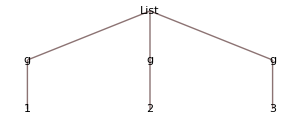

```mathematica
{g[1],g[2],g[3]}//TreeForm[#,AspectRatio->0.4,ImageSize->300]&
```

{f[g[1]],f[g[2]],f[g[3]]}

{f[g[f[1]]],f[g[f[2]]],f[g[f[3]]]}

{g[f[1]],g[f[2]],g[f[3]]}

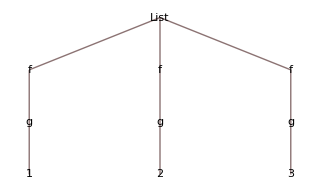
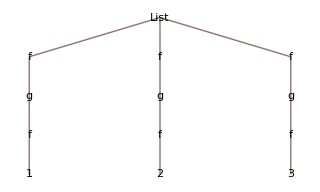
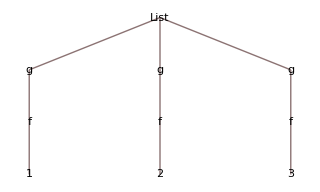

```mathematica
Map[Style[f,Red],{g[1],g[2],g[3]},1](*Applies f to level one, i.e. f[g[i]]*)
Map[Style[f,Red],{g[1],g[2],g[3]},2](*Applies f to levels 1 and 2, i.e. g[f[i]]*)
Map[Style[f,Red],{g[1],g[2],g[3]},{2}](*Applies f only to level 2, i.e. g[f[i]]*)
TreeForm[#,AspectRatio->0.6,ImageSize->320]&/@{%%%,%%,%}//Row
```

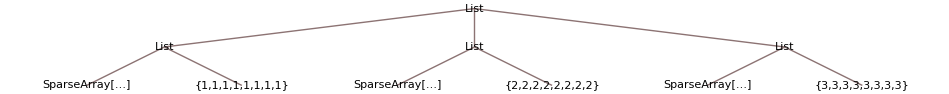

```mathematica
array={{matrix,ConstantArray[1,8]},{matrix,ConstantArray[2,8]},{matrix,ConstantArray[3,8]}};
array//TreeForm[#,2,AspectRatio->0.1]&
```

```mathematica
Map[MatrixForm,array,{2}](*Apply MatrixForm specifically at the 2nd level of array*)
```

{{(2 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 2 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 2 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 2 | -1 | 0 | -1
0 | 0 | 0 | 0 | -1 | 2 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 2 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 2),(1
1
1
1
1
1
1
1)},{(2 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 2 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 2 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 2 | -1 | 0 | -1
0 | 0 | 0 | 0 | -1 | 2 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 2 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 2),(2
2
2
2
2
2
2
2)},{(2 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 2 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 2 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 2 | -1 | 0 | -1
0 | 0 | 0 | 0 | -1 | 2 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 2 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 2),(3
3
3
3
3
3
3
3)}}

## WorkingPrecision / AccuracyGoal / PrecisionGoal

```mathematica
?WorkingPrecision
```

```mathematica
MachinePrecision//N
```

15.9546

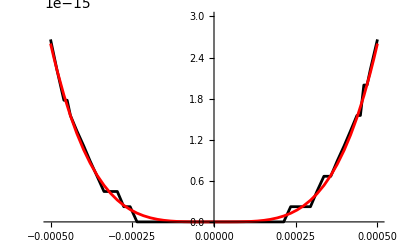

```mathematica
Clear[f]
f[x_?NumberQ]:=x^2/2+Cos[x]-1
Show[Plot[f[x],{x,-5 10^-4,5 10^-4},PlotRange->{0,3 10^-15},WorkingPrecision->#[[1]],PlotStyle->#[[2]]]&/@{{MachinePrecision,Black},{25,Red}}]
```

```mathematica
FindMinimum[f[x],{x}]
FindMinimum[f[x],{x},WorkingPrecision->25]
```

{3.90132×10^-13,{x→0.00174925}}

{0,{x→-7.152225495468876285027848×10^-13}}

AccuracyGoal vs PrecisionGoal

AccuracyGoalpaclet:ref/AccuracyGoal effectively specifies the absolute error allowed in a numerical procedure. 
PrecisionGoalpaclet:ref/PrecisionGoal effectively specifies the relative error allowed in a numerical procedure. 

AccuracyGoalpaclet:ref/AccuracyGoal->a  
PrecisionGoalpaclet:ref/PrecisionGoal->p
⇒ attempts to make the numerical error in a result of size x be less than 10^-a+|x|10^-p.

```mathematica
?AccuracyGoal (*normally equal to half the setting for WorkingPrecisionpaclet:ref/WorkingPrecision*)
(*In most cases,you must set WorkingPrecision paclet:ref/WorkingPrecisionto be at least as large as AccuracyGoalpaclet:ref/AccuracyGoal*)
```

```mathematica
?PrecisionGoal(*normally equal to half the setting for WorkingPrecisionpaclet:ref/WorkingPrecision*)
(*In most cases,you must set WorkingPrecisionpaclet:ref/WorkingPrecision to be at least as large as PrecisionGoalpaclet:ref/PrecisionGoal*)
```

Example:

```mathematica
Clear[f]
f[x_]:=Sin[x^2]
FindMinimum[f[x],{x,2}]
FindMinimum[f[x],{x,2},AccuracyGoal->18,PrecisionGoal->20](*error ≤ 10^-18 + x·10^-20 ; WorkingPrecision->MachinePrecision*)
FindMinimum[f[x],{x,2},AccuracyGoal->18,PrecisionGoal->20,WorkingPrecision->5](*WorkingPrecision < MachinePrecision, but now it doesn't complain--why?!*)
```

{-1.,{x→2.1708}}

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-1.,{x→2.1708}}

{-1.,{x→2.1708}}

WorkingPrecision -> MachinePrecision  [16 digits, but untracked]
With MachinePrecision, Mathematica uses the usual floating-point hardware (i.e. as if you were using Doubles in other languages).

WorkingPrecision -> n   [n digits, fully tracked]
With an explicit value, Mathematica uses its own software-implemented arbitrary precision arithmetic (i.e. it keeps an estimate of significance/error; it does extra work to make sure you’re satisfying your precision requirements; keep in mind that this also means it can be slower).

The warning of FindMinimum was not a WorkingPrecision problem; it was Mathematica telling us that it did not track the precision with its extra software, so it cannot guarantee that AccuracyGoal and PrecisionGoal were met.

## Kernels

Different notebooks doesn’t necessarily mean different Kernels. 
By default, they all run on the same Kernel--think of different ‘windows’ to the same ‘computing center’.

To create separate Kernels: Evaluation -> Kernel Configuration Options

To change notebook’s Kernel: Evaluation -> Notebook’s Kernel -> [Select Kernel]

To quit specific Kernel: Evaluation -> Quit Kernel -> [Select Kernel]

It is also useful to know how to abort an Evaluation: Evaluation -> Abort Evaluation (shortcut: Cmd + .)

We will see later how to use different Kernels to run computations in Parallel.

## Working with Data

```mathematica
Quit[]
```

```mathematica
y[t_]:=y0+v0 t-1/2 g t^2;
par={y0->0,v0->10,g->9.8};
```

```mathematica
(*you can access Wolfram's 'knowledge' with Ctrl+= *)
```

9.8 m/s^2

1.6232 m/s^2

2.176×10^-8 kg

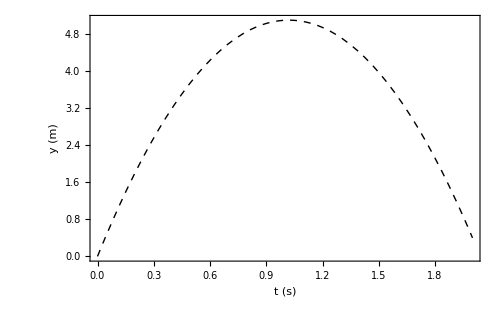

```mathematica
theory…plot=Plot[y[t]/.par,{t,0,2},PlotStyle->{Black,Dashed,AbsoluteThickness[1]},Frame->True,
FrameLabel->{Style["t (s)",16,FontFamily->"Times"], Style["y (m)",16,FontFamily->"Times"]},
FrameTicksStyle->Directive[14,FontFamily->"Times"],ImageSize->500]
```

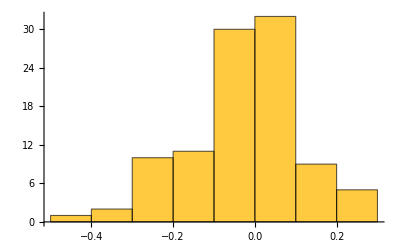

```mathematica
Histogram[RandomVariate[NormalDistribution[0,0.15],100]]
```

```mathematica
data=Table[{t,Around[y[t]+RandomVariate[NormalDistribution[0,0.15]],0.15]/.par},{t,0,2,0.1}]
```

{{0.,0.020.15},{0.1,0.910.15},{0.2,1.740.15},{0.3,2.570.15},{0.4,2.870.15},{0.5,3.660.15},{0.6,4.300.15},{0.7,4.560.15},{0.8,4.750.15},{0.9,4.910.15},{1.,5.170.15},{1.1,5.510.15},{1.2,4.990.15},{1.3,4.910.15},{1.4,4.400.15},{1.5,4.030.15},{1.6,3.500.15},{1.7,2.880.15},{1.8,2.220.15},{1.9,1.390.15},{2.,0.670.15}}

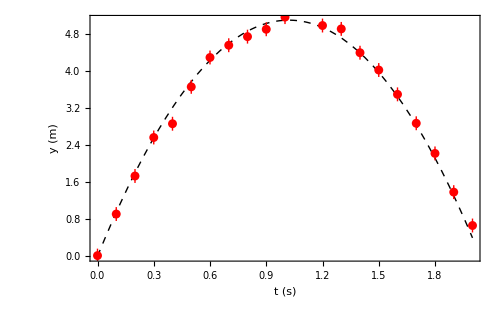

```mathematica
Show[theory…plot,ListPlot[data,PlotStyle->Red]]
```

```mathematica
x//f
```

f[2]

```mathematica
f[#]&@x
x//f[#]&
```

f[2]

f[2]

```mathematica
Prepend[data,{"t (s)","y (m)"}]//Grid[#,Spacings->{1, 1},Frame->All,Background->{None,{LightGray}}]&
```

t (s) | y (m)
0. | 0.020.15
0.1 | 0.910.15
0.2 | 1.740.15
0.3 | 2.570.15
0.4 | 2.870.15
0.5 | 3.660.15
0.6 | 4.300.15
0.7 | 4.560.15
0.8 | 4.750.15
0.9 | 4.910.15
1. | 5.170.15
1.1 | 5.510.15
1.2 | 4.990.15
1.3 | 4.910.15
1.4 | 4.400.15
1.5 | 4.030.15
1.6 | 3.500.15
1.7 | 2.880.15
1.8 | 2.220.15
1.9 | 1.390.15
2. | 0.670.15

```mathematica
SetDirectory[NotebookDirectory[]];
Export["data.csv",data]
SystemOpen["data.csv"]
```

data.csv

```mathematica
{#[[1]],#[[2]][[1]],#[[2]][[2]]}&@data[[1]]
```

{0.,-0.0957018,0.15}

```mathematica
data…export=Prepend[{#[[1]],#[[2]][[1]],#[[2]][[2]]}&/@data,{"t","y","dy"}] (*change format of data for exporting*)
```

{{t,y,dy},{0.,0.0169891,0.15},{0.1,0.914511,0.15},{0.2,1.73623,0.15},{0.3,2.56809,0.15},{0.4,2.86507,0.15},{0.5,3.66202,0.15},{0.6,4.29595,0.15},{0.7,4.56078,0.15},{0.8,4.74644,0.15},{0.9,4.90561,0.15},{1.,5.16814,0.15},{1.1,5.51359,0.15},{1.2,4.98634,0.15},{1.3,4.91372,0.15},{1.4,4.39915,0.15},{1.5,4.02543,0.15},{1.6,3.49963,0.15},{1.7,2.87521,0.15},{1.8,2.22391,0.15},{1.9,1.38783,0.15},{2.,0.666872,0.15}}

```mathematica
Export["data.csv",data…export]
SystemOpen["data.csv"]
```

data.csv

```mathematica
{#[[1]],Around[#[[2]],#[[3]]]}&/@Import["data.csv"](*change format of imported data to use Around[]*)
```

{{0.,-0.100.15},{0.1,0.720.15},{0.2,1.680.15},{0.3,2.440.15},{0.4,3.220.15},{0.5,3.680.15},{0.6,4.150.15},{0.7,4.730.15},{0.8,5.170.15},{0.9,4.850.15},{1.,5.090.15},{1.1,5.330.15},{1.2,5.140.15},{1.3,4.750.15},{1.4,4.610.15},{1.5,3.900.15},{1.6,3.210.15},{1.7,2.780.15},{1.8,2.260.15},{1.9,1.220.15},{2.,0.540.15}}

```mathematica
Show[theory…plot,ListPlot[data,PlotStyle->Red]]
```

-Graphics-

```mathematica
data[[1]]
```

{0.,-0.100.15}

```mathematica
f…interpolation=Interpolation[{#[[1]],#[[2]][[1]]}&/@data]
```

InterpolatingFunction[…]

```mathematica
f…interpolation//FullForm (*check later*)
```

InterpolatingFunction[List[List[0.,2.]],List[5,7,0,List[21],List[4],0,0,0,0,Automatic,List[],List[],False],List[List[0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.]],List[Developer`PackedArrayForm,List[0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21],List[-0.0957018,0.724839,1.67882,2.43685,3.22495,3.6817,4.14565,4.72782,5.16758,4.84695,5.08643,5.32867,5.14351,4.74725,4.60861,3.8973,3.21329,2.77604,2.26373,1.22045,0.543344]],List[Automatic]]

```mathematica
theory…plot//FullForm
```

Graphics[List[Annotation[List[List[List[List[],List[],Annotation[List[Directive[Opacity[1.],GrayLevel[0],Dashing[List[Small,Small]],AbsoluteThickness[1]],Line[List[List[4.08163×10^-8,4.08163×10^-7],List[0.000613436,0.00613251],List[0.00122683,0.0122609],List[0.00245362,0.0245067],List[0.0049072,0.048954],List[0.00981436,0.0976716],List[0.0196287,0.194399],List[0.0392573,0.385022],List[0.0818167,0.785367],List[0.121556,1.14316],List[0.160515,1.4789],List[0.202777,1.82629],List[0.242218,2.1347],List[0.284962,2.45172],List[0.326926,2.74554],List[0.366069,3.00406],List[0.408515,3.26741],List[0.44814,3.49734],List[0.486986,3.7078],List[0.529134,3.91942],List[0.568461,4.10119],List[0.611091,4.28109],List[0.652941,4.44038],List[0.691971,4.57347],List[0.734303,4.70095],List[0.773815,4.80408],List[0.774484,4.80569],List[0.775152,4.8073],List[0.77649,4.81051],List[0.779166,4.81687],List[0.784518,4.82938],List[0.795221,4.85357],List[0.816628,4.89856],List[0.817285,4.89987],List[0.817942,4.90118],List[0.819255,4.90377],List[0.821883,4.90892],List[0.827137,4.91901],List[0.837645,4.93837],List[0.838302,4.93954],List[0.838959,4.94071],List[0.840272,4.94304],List[0.8429,4.94765],List[0.848154,4.95665],List[0.858662,4.97385],List[0.859275,4.97482],List[0.859888,4.97578],List[0.861113,4.9777],List[0.863564,4.9815],List[0.868466,4.98892],List[0.878269,5.00304],List[0.878882,5.0039],List[0.879495,5.00474],List[0.88072,5.00643],List[0.883171,5.00975],List[0.888073,5.01623],List[0.897876,5.02847],List[0.898541,5.02927],List[0.899205,5.03006],List[0.900534,5.03163],List[0.903191,5.03472],List[0.908505,5.04068],List[0.919134,5.05178],List[0.919799,5.05244],List[0.920463,5.05309],List[0.921791,5.05439],List[0.924449,5.05692],List[0.929763,5.06178],List[0.940392,5.07067],List[0.941012,5.07115],List[0.941633,5.07163],List[0.942873,5.07258],List[0.945354,5.07444],List[0.950316,5.07797],List[0.950936,5.07839],List[0.951557,5.07881],List[0.952797,5.07964],List[0.955278,5.08126],List[0.96024,5.0843],List[0.96086,5.08467],List[0.961481,5.08503],List[0.962721,5.08573],List[0.965202,5.08711],List[0.970164,5.08967],List[0.970784,5.08997],List[0.971404,5.09027],List[0.972645,5.09086],List[0.975126,5.09199],List[0.980088,5.09407],List[0.980696,5.09431],List[0.981304,5.09455],List[0.98252,5.09501],List[0.984952,5.09588],List[0.98556,5.09609],List[0.986168,5.0963],List[0.987385,5.0967],List[0.989817,5.09746],List[0.990425,5.09764],List[0.991033,5.09781],List[0.992249,5.09816],List[0.994681,5.0988],List[0.995289,5.09895],List[0.995897,5.0991],List[0.997114,5.09938],List[0.999546,5.09991],List[1.00015,5.10003],List[1.00076,5.10015],List[1.00198,5.10038],List[1.00259,5.10048],List[1.00319,5.10059],List[1.00441,5.10079],List[1.00502,5.10088],List[1.00563,5.10097],List[1.00684,5.10114],List[1.00745,5.10122],List[1.00806,5.10129],List[1.00927,5.10143],List[1.00988,5.1015],List[1.01049,5.10156],List[1.0111,5.10162],List[1.01171,5.10167],List[1.01232,5.10172],List[1.01292,5.10177],List[1.01353,5.10181],List[1.01414,5.10185],List[1.01475,5.10188],List[1.01536,5.10192],List[1.01596,5.10194],List[1.01657,5.10197],List[1.01718,5.10199],List[1.01779,5.10201],List[1.0184,5.10202],List[1.019,5.10203],List[1.01966,5.10204],List[1.02032,5.10204],List[1.02098,5.10204],List[1.02164,5.10203],List[1.0223,5.10202],List[1.02296,5.10201],List[1.02362,5.10199],List[1.02428,5.10197],List[1.02494,5.10194],List[1.0256,5.10191],List[1.02626,5.10187],List[1.02692,5.10183],List[1.02758,5.10179],List[1.02824,5.10174],List[1.02956,5.10163],List[1.03022,5.10157],List[1.03088,5.1015],List[1.0322,5.10136],List[1.03286,5.10128],List[1.03352,5.1012],List[1.03484,5.10102],List[1.0355,5.10093],List[1.03616,5.10083],List[1.03747,5.10061],List[1.04011,5.10014],List[1.04077,5.10001],List[1.04143,5.09987],List[1.04275,5.09959],List[1.04539,5.09898],List[1.04605,5.09882],List[1.04671,5.09865],List[1.04803,5.0983],List[1.05067,5.09755],List[1.05133,5.09736],List[1.05199,5.09715],List[1.05331,5.09674],List[1.05594,5.09585],List[1.06122,5.09388],List[1.06184,5.09363],List[1.06245,5.09338],List[1.06368,5.09286],List[1.06615,5.09179],List[1.07107,5.08946],List[1.07169,5.08916],List[1.0723,5.08884],List[1.07353,5.08821],List[1.076,5.0869],List[1.08092,5.0841],List[1.08154,5.08373],List[1.08215,5.08336],List[1.08338,5.08261],List[1.08585,5.08106],List[1.09077,5.07778],List[1.10062,5.07051],List[1.10129,5.06999],List[1.10195,5.06946],List[1.10329,5.06838],List[1.10596,5.06618],List[1.11129,5.06156],List[1.12197,5.0515],List[1.12264,5.05083],List[1.1233,5.05016],List[1.12464,5.04881],List[1.12731,5.04605],List[1.13264,5.04032],List[1.14332,5.02802],List[1.14397,5.02722],List[1.14463,5.02643],List[1.14594,5.02483],List[1.14856,5.02157],List[1.1538,5.01485],List[1.16428,5.00061],List[1.16494,4.99969],List[1.16559,4.99876],List[1.1669,4.99689],List[1.16952,4.99309],List[1.17476,4.9853],List[1.18524,4.96891],List[1.18585,4.96792],List[1.18646,4.96693],List[1.18768,4.96493],List[1.19013,4.9609],List[1.19502,4.95265],List[1.20479,4.93546],List[1.22434,4.89826],List[1.225,4.89693],List[1.22567,4.8956],List[1.22699,4.89293],List[1.22964,4.88753],List[1.23494,4.87652],List[1.24554,4.85368],List[1.26674,4.80471],List[1.30632,4.70147],List[1.34513,4.58537],List[1.38723,4.4427],List[1.42652,4.29392],List[1.4691,4.11554],List[1.50887,3.93294],List[1.54785,3.73886],List[1.59014,3.51151],List[1.62961,3.28351],List[1.67238,3.0192],List[1.71437,2.74227],List[1.75354,2.46836],List[1.79601,2.15437],List[1.83567,1.84527],List[1.87454,1.52729],List[1.91671,1.16555],List[1.95607,0.812284],List[1.95676,0.805988],List[1.95744,0.799687],List[1.95881,0.787071],List[1.96156,0.761783],List[1.96705,0.710987],List[1.97803,0.608507],List[1.97872,0.602062],List[1.97941,0.595614],List[1.98078,0.582702],List[1.98353,0.556823],List[1.98902,0.504845],List[1.9897,0.498326],List[1.99039,0.491804],List[1.99176,0.478744],List[1.99451,0.45257],List[1.99519,0.446015],List[1.99588,0.439455],List[1.99725,0.426322],List[1.99794,0.419749],List[1.99863,0.413171],List[1.99931,0.406588],List[2.,0.4]]]],"Charting`Private`Tag#1"]]],List[]],Association[Rule["HighlightElements",Association[Rule["Label",List["XYLabel"]],Rule["Ball",List["InterpolatedBall"]]]],Rule["LayoutOptions",Association[Rule["PanelPlotLayout",Association[]],Rule["PlotRange",List[List[0,2],List[0.,5.10204]]],Rule["Frame",List[List[True,True],List[True,True]]],Rule["AxesOrigin",List[0,0]],Rule["ImageSize",List[500,Times[500,Power[GoldenRatio,-1]]]],Rule["Axes",List[True,True]],Rule["LabelStyle",List[]],Rule["AspectRatio",Power[GoldenRatio,-1]],Rule["DefaultStyle",List[Directive[Opacity[1.],GrayLevel[0],Dashing[List[Small,Small]],AbsoluteThickness[1]]]],Rule["HighlightLabelingFunctions",Association[Rule["CoordinatesToolOptions",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]],Rule["ScalingFunctions",List[List[Identity,Identity],List[Identity,Identity]]]]],Rule["Primitives",List[]],Rule["GCFlag",False]]],Rule["Meta",Association[Rule["DefaultHighlight",List["Dynamic",None]],Rule["Index",List[]],Rule["Function",Plot],Rule["GroupHighlight",False]]]],"DynamicHighlight"]],List[Rule[DisplayFunction,Identity],RuleDelayed[PlotInteractivity,$PlotInteractivity],Rule[DisplayFunction,Identity],RuleDelayed[PlotInteractivity,$PlotInteractivity],Rule[DefaultBaseStyle,List["PlotGraphics","Graphics"]],Rule[DisplayFunction,Identity],Rule[Ticks,List[Automatic,Automatic]],Rule[AxesOrigin,List[0,0]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],RuleDelayed[PlotInteractivity,$PlotInteractivity],Rule[DefaultBaseStyle,List["PlotGraphics","Graphics"]],Rule[DisplayFunction,Identity],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.05],Scaled[0.05]]]],Rule[PlotRangeClipping,True],Rule[ImagePadding,All],RuleDelayed[PlotInteractivity,$PlotInteractivity],Rule[DisplayFunction,Identity],RuleDelayed[PlotInteractivity,$PlotInteractivity],Rule[DefaultBaseStyle,List["PlotGraphics","Graphics"]],Rule[AspectRatio,Power[GoldenRatio,-1]],Rule[Axes,List[True,True]],Rule[AxesLabel,List[None,None]],Rule[AxesOrigin,List[0,0]],RuleDelayed[DisplayFunction,Identity],Rule[Frame,List[List[True,True],List[True,True]]],Rule[FrameLabel,List[List[HoldForm[Style["y (m)",16,Rule[FontFamily,"Times"]]],None],List[HoldForm[Style["t (s)",16,Rule[FontFamily,"Times"]]],None]]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[FrameTicksStyle,Directive[14,Rule[FontFamily,"Times"]]],Rule[GridLines,List[None,None]],Rule[GridLinesStyle,Directive[GrayLevel[0.5,0.4]]],Rule[ImageSize,500],Rule[Method,List[Rule["DefaultBoundaryStyle",Automatic],Rule["DefaultGraphicsInteraction",List[Rule["Version",1.2],Rule["TrackMousePosition",List[True,False]],Rule["Effects",List[Rule["Highlight",List[Rule["ratio",2]]],Rule["HighlightPoint",List[Rule["ratio",2]]],Rule["Droplines",List[Rule["freeformCursorMode",True],Rule["placement",List[Rule["x","All"],Rule["y","None"]]]]]]]]],Rule["DefaultMeshStyle",AbsolutePointSize[6]],Rule["ScalingFunctions",None],Rule["CoordinatesToolOptions",List[Rule["DisplayFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]],Rule["CopiedValueFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]]]]]],Rule[PlotRange,List[List[0,2],List[0.,5.10204]]],Rule[PlotRangeClipping,True],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.02],Scaled[0.02]]]],Rule[Ticks,List[Automatic,Automatic]]]]

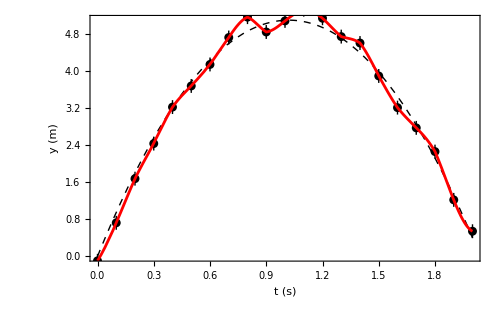

```mathematica
Show[theory…plot,ListPlot[data,PlotStyle->Black],Plot[f…interpolation[t],{t,0,2},PlotStyle->Red]]
```

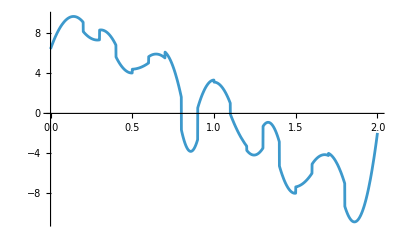

```mathematica
Plot[f…interpolation'[t],{t,0,2}](*Taking derivatives of interpolation functions can be tricky*)
```

```mathematica
?Fit
```

```mathematica
Clear[f…fitted]
Fit[data,{1,t,t^2},{t}](*Fit uses information about uncertainty*)
f…fitted[t_]=Fit[data,{1,t,t^2},{t}]/.{Around[a_,b_]:>a}(*To plot the best fit, we need to take the best fit values, without uncertainty*)
```

t^2 (-4.880.10)+(-0.080.09)+t (10.080.21)

-0.0833198+10.0787 t-4.87704 t^2

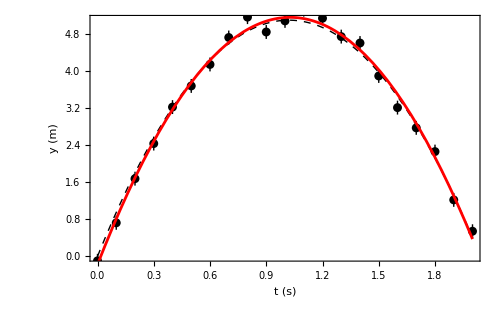

```mathematica
Show[theory…plot,ListPlot[data,PlotStyle->Black],Plot[f…fitted[t],{t,0,2},PlotStyle->Red]]
```

```mathematica
fit=LinearModelFit[data,{1,t,t^2/2},{t}](*LinearModelFit gives more detailed information about the fit*)
```

FittedModel[…]

```mathematica
fit["BestFit"]
```

-0.178328+10.3987 t-5.06134 t^2

```mathematica
fit["ParameterEstimates"]
```

```mathematica
data
```

{{0.,-0.100.15},{0.1,0.720.15},{0.2,1.680.15},{0.3,2.440.15},{0.4,3.220.15},{0.5,3.680.15},{0.6,4.150.15},{0.7,4.730.15},{0.8,5.170.15},{0.9,4.850.15},{1.,5.090.15},{1.1,5.330.15},{1.2,5.140.15},{1.3,4.750.15},{1.4,4.610.15},{1.5,3.900.15},{1.6,3.210.15},{1.7,2.780.15},{1.8,2.260.15},{1.9,1.220.15},{2.,0.540.15}}

Running external code with exported data and importing results

```mathematica
FileNames[]/.{a_String:>Style[a,Red]/;StringContainsQ[a,".py"]||StringContainsQ[a,".csv"]}//TableForm
```

data.csv
diagrams.pdf
.DS_Store
fit_parameters.csv
Lecture-1.nb
Lecture-2.nb
Lecture-3.nb
Lecture-4.nb
python-fit.py
wave.mov

```mathematica
SystemOpen["python-fit.py"]
```

```mathematica
RunProcess[{"/opt/miniconda3/bin/python3","python-fit.py"},"StandardOutput"]
```

Best fit parameters:
y0 = -0.178 +- 0.090
v0 = 10.399 +- 0.207
g = 10.123 +- 0.200
Saved best-fit parameters to fit_parameters.csv

```mathematica
(#[[1]]->#[[2]])&/@Import["fit_parameters.csv"][[2;;]]
%//FullForm (*y0,v0,g are given as Strings with "..." *)
```

{y0→-0.178328,v0→10.3987,g→10.1227}

List[Rule["y0",-0.178328],Rule["v0",10.3987],Rule["g",10.1227]]

```mathematica
imported…par=(#[[1]]->#[[2]])&/@Import["fit_parameters.csv"][[2;;]]/.{a_String:>ToExpression[a]}
%FullForm
```

{y0→-0.178328,v0→10.3987,g→10.1227}

{FullForm (y0→-0.178328),FullForm (v0→10.3987),FullForm (g→10.1227)}

```mathematica
Show[theory…plot,ListPlot[data,PlotStyle->Black],Plot[y[t]/.imported…par,{t,0,2},PlotStyle->Red]]
```

-Graphics-

## Fun with Datasets...Titanic

9.8 m/s^2

```mathematica
//FullForm
```

EntityClass["Particle","FundamentalParticles"]

```mathematica
particles=EntityList[]
```

{bottom quark,bottom antiquark,charm quark,charm antiquark,down quark,down antiquark,electron,electron neutrino,electron antineutrino,gluon,graviton,Higgs boson,muon,anti-muon,muon neutrino,muon antineutrino,photon,positron,strange quark,strange antiquark,tau,anti-tau,tau neutrino,tau antineutrino,top quark,top antiquark,up quark,up antiquark,Z boson,W- boson,W+ boson}

```mathematica
Entity["Particle","BottomQuark"]["Type"]
Entity["Particle","BottomQuark"]["Mass"]
Entity["Particle","BottomQuark"]["Memberships"]
Entity["Particle",{"WBoson",-1}]["DecayModes"]
```

Quark

4.18 GeV/c^2

{charged subatomic particles,fermion,fundamental particles,quark}

<|{π^-,photon}→0..Interval[{0,0.0002}],{(D̄)_s,photon}→0.,{charm antiquark}→0.334,{charm antiquark,strange quark}→0.31|>

```mathematica
?TabView
```

```mathematica
TabView[#["FullSymbol"]->#["Dataset"]&/@particles,ControlPlacement->Top]
```

12345678910111213141516171819202122232425262728293031

Titanic data

```mathematica
?ExampleData
```

```mathematica
titanic= ExampleData[{"Dataset","Titanic"}];
```

```mathematica
titanic//Length
titanic//Dataset
```

1309

```mathematica
Count[titanic[All,"survived"],True]
Count[titanic[All,"sex"],"male"]
Count[titanic[All,"sex"],"female"]
Count[titanic[All,"class"],"1st"]
```

500

843

466

323